```mathematica
ClearAll["Global`*"]
```

```mathematica
(* For the prereheting scenario with inflaton potential , 
we study numerically the daughter mode function  and number density  for a fixed momentum ,
showing the equivalence with the Mathieu equation. Then, we compute the mode function and number density for a fixed  in which the dynamics presents resonance. This is checked looking at the stability/instability chart. *)
```

```mathematica
Mpl=1.0;                    (* reduced mass Planck *)
mϕ=1.0;                      (* inflation mass *)
g=200.0;                    (* coupling constant ϕ-χ *)
k=1.0;                        (* comoving momentum for χ *)
tMax=50.0;               (* Time *)
Φ=0.1 Mpl;                (* Initial amplitude ϕ *)
```

## Daughter dynamic:

```mathematica
(* Frequency *)
ω2[t_]:=k^2+g^2 Φ^2 Sin[mϕ t]^2;
ω[t_]:=√ω2[t];

(* EOM daughter χ *)
eqχ=χ''[t]+ω2[t]*χ[t]==0;

(*Initial conditions*)
χconditions={χ[0]==1/(√(2ω[0])),χ'[0]==-I*√(ω[0]/2)}; (* Initial conditions  to be valued at  *)

(*Solve χ dynamic *)
solχ=NDSolve[{eqχ,χconditions[[1]],χconditions[[2]]},χ,{t,0,tMax},MaxSteps->Infinity,Method->"StiffnessSwitching"];

(* Solution χ *)
χsol[t_]:=Evaluate[χ[t]/. solχ[[1]]];

(* Number particles *)
numbχ[t_]:=1/2 Abs[χ'[t]]^2/ω[t]+ω[t]/2 Abs[χ[t]]^2-1/2
numbχsol[t_]:=Evaluate[numbχ[t]/. solχ[[1]]];
```

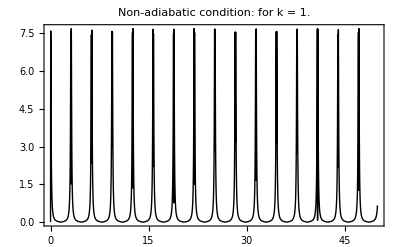

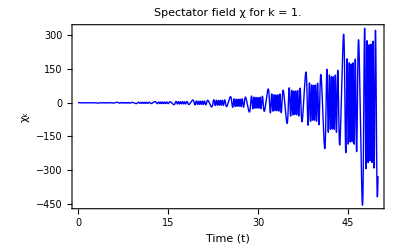

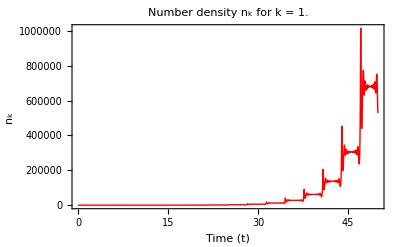

```mathematica
(*Plots *)
Plot[ Abs[ω'[t]]/ω2[t],{t,0,tMax},PlotRange->All,PlotStyle->{Thick,Black},Frame->True,PlotLabel->Style[StringForm["Non-adiabatic condition:  for k = ``",k],12]]
Plot[Re[χsol[t]],{t,0,tMax},PlotRange->All,PlotStyle->{Thick ,Blue},Frame->True,FrameLabel->{"Time (t)","χ_k"},PlotLabel->Style[StringForm["Spectator field χ for k = ``",k],12]]
Plot[numbχsol[t],{t,0,tMax},PlotRange->All,PlotStyle->{Thick,Red},Frame->True,FrameLabel->{"Time (t)","n_k"},PlotLabel->Style[StringForm["Number density n_k for k = ``",k],12]]
```

## Check equivalence with Mathieu equation: ,

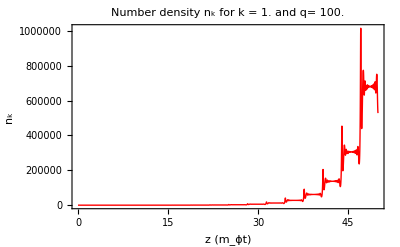

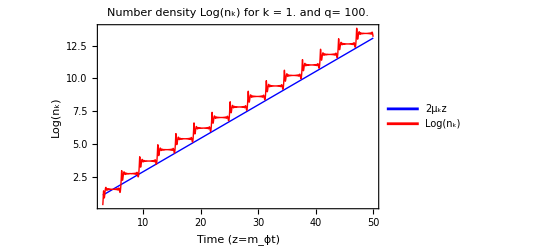

```mathematica
(* Map to Mathieu equation *)
q = (g^2 Φ^2)/(4 mϕ^2);
A = k^2/mϕ^2+2q;

(* Mathieu equation for the daughter field *)
eqχMathieu = χnew''[z] + (A - 2q Cos[2 z])χnew[z]==0;

(* Solve it *)
solχMathieu = NDSolve[{eqχMathieu,χnew[0]==1/(√(2 √(A - 2 q Cos[0]))),χnew'[0]==-I*√((√(A - 2 q Cos[0]))/2)},χnew,{z,0, mϕ*tMax},MaxSteps->Infinity,Method->"StiffnessSwitching"];

χnewsol[z_]:=Evaluate[χnew[z]/.solχMathieu[[1]]];

(* Number particles *)
numbχnewsol[z_]:=1/2 Abs[χnewsol'[z]]^2/(√(A - 2 q Cos[2 z]))+(√(A - 2 q Cos[2 z]))/2 Abs[χnewsol[z]]^2-1/2
y= 2*Abs[Im[MathieuCharacteristicExponent[A,q]]]*z;

(* Plot *)
Plot[numbχnewsol[z],{z,0,mϕ*tMax},PlotRange->All,PlotStyle->{Thick,Red},Frame->True,FrameLabel->{"z (m_ϕt)","n_k"},PlotLabel->Style[StringForm["Number density n_k for k = `` and q= ``",k,q],12]]

μplot = Plot[y+ Log[numbχnewsol[3]],{z,3,tMax},PlotRange->All,PlotStyle->{Thick,Blue},PlotLegends->{"2μ_kz"},Frame->True];
nplot = Plot[Log[numbχnewsol[z]],{z,3,tMax},PlotRange->All,PlotStyle->{Thick,Red},PlotLegends->{"Log(n_k)"},Frame->True];
Show[μplot,nplot,FrameLabel->{"Time (z=m_ϕt)","Log(n_k)"},PlotLabel->Style[StringForm["Number density Log(n_k) for k = `` and q= ``",k,q],12]]
```

## Stability / Instability chart

```mathematica
(* Look that the  mode chosen for the specific  (and consequentely ) value fits in the resonance region. For , chosing  we sit in a resonance band (see the figure). This implies that the previous plots for the mode function and number density grows exponentially  *)
```

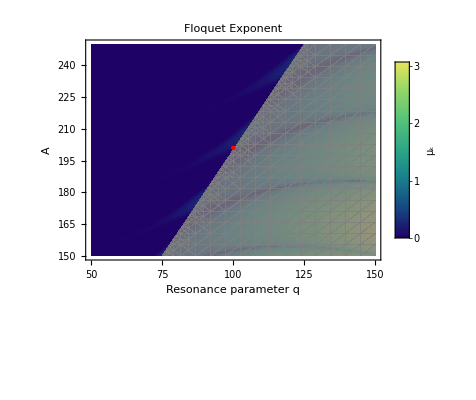

```mathematica
qMaxChart=150;
AMaxChart=250;

μ[A_,q_]:=Abs[Im[MathieuCharacteristicExponent[A,q]]];

plotFloquet=DensityPlot[μ[A,q],{q,50,qMaxChart},{A,150,AMaxChart},PlotPoints->80,MaxRecursion->2,ColorFunction->"BlueGreenYellow",PlotRange->All,PlotLegends->BarLegend[Automatic,LegendLabel->"μ_k"],FrameLabel->{"Resonance parameter q","A"},PlotLabel->"Floquet Exponent"];
unphysicalRegion=RegionPlot[A<2*q,{q,50,qMaxChart},{A,150,AMaxChart},BoundaryStyle->None,PlotStyle->Directive[Gray,Opacity[0.8]]];
PointK = ListPlot[{{q,A}},PlotStyle->{Red,PointSize[Large]}];

Show[plotFloquet,PointK,unphysicalRegion,Epilog->Text[Style["Unphysical (k^2 < 0)",Black,Bold,14],{qMaxChart*0.7,qMaxChart*0.7}]]
```